```mathematica
ClearAll["Global`*"]
export=False;
```

```mathematica
(* I added to an all things hydrogen package
that had written previously located 
here https://github.com/cphys/atomicOrbitals *)
<<"atomSurfaceInteractions`"
ParallelNeeds["atomSurfaceInteractions`"]
<<"hydrogenAtom`"
ParallelNeeds["hydrogenAtom`"]
<<"cmTab`"
<<"cmTix`"
```

```mathematica
(* Import NIST data *)
nistDataNR=Import[FileNameJoin[{NotebookDirectory[],"nistDataNR.csv"}],"CSV"];
nistData=Import[FileNameJoin[{NotebookDirectory[],"nistData.csv"}],"CSV"];
```

```mathematica
(* Here all oscillator strengths are calculated 
   (the rest is just formatting) *)
valuesNR=ParallelTable[hydrogenOscillatorsNR[n],{n,2,40}];
values=Flatten[ParallelTable[Prepend[#,ToString[n]]&/@MapThread[Prepend,{hydrogenOscillators[n],{"1/2","3/2"}}],{n,2,6}],1];
```

```mathematica
(* Rounding and formatting *)
valuesFNR=Table[{
ToString[i+1],
NumberForm[valuesNR[[i]][[1]],{6,6}],
NumberForm[valuesNR[[i]][[2]],{6,6}]},
{i,Length[valuesNR]}];

valuesF=Table[{
values[[i]][[1]],
values[[i]][[2]],
NumberForm[values[[i]][[3]],{6,6}],
NumberForm[values[[i]][[4]],{5,5}]},
{i,Length[values]}];
```

```mathematica
pDiff[f1_,f2_]:=NumberForm[Abs[f2-f1]/f1*100,{7,5}]
```

```mathematica
(* Calculate % differences between our calculations and NIST data *)
pdifsNR=
Table[
{pDiff[valuesNR[[i]][[1]],nistDataNR[[i]][[1]]],pDiff[valuesNR[[i]][[2]],nistDataNR[[i]][[2]]]},{i,Length[valuesNR]}];
pdifs=Table[
{pDiff[values[[i]][[-2]],nistData[[i]][[1]]],pDiff[values[[i]][[-1]],nistData[[i]][[2]]]},
{i,Length[values]}];
```

```mathematica
appendF[m1_,m2_]:=FlattenAt[#,-1]&/@MapThread[Append,{m1,m2}]
```

```mathematica
Grid[Prepend[
Fold[appendF,valuesFNR,{nistDataNR,pdifsNR}],
{"n","E_n0","f_n0","E_n0 (NIST)","f_n0(NIST)","% diff E_n0","% diff f_n0"}],
Dividers->All]
```

n | E_n0 | f_n0 | E_n0 (NIST) | f_n0(NIST) | % diff E_n0 | % diff f_n0
2 | 0.374801 | 0.415975 | 0.3748 | 0.4164 | 0.00036 | 0.10228
3 | 0.444209 | 0.079060 | 0.444207 | 0.079142 | 0.00045 | 0.10425
4 | 0.468502 | 0.028976 | 0.4685 | 0.029006 | 0.00036 | 0.10472
5 | 0.479746 | 0.013931 | 0.479744 | 0.013945 | 0.00036 | 0.10081
6 | 0.485854 | 0.007795 | 0.485852 | 0.0078035 | 0.00033 | 0.10443
7 | 0.489536 | 0.004811 | 0.489535 | 0.0048164 | 0.00030 | 0.10393
8 | 0.491927 | 0.003182 | 0.491925 | 0.003185 | 0.00036 | 0.10244
9 | 0.493566 | 0.002215 | 0.493564 | 0.0022172 | 0.00032 | 0.10232
10 | 0.494738 | 0.001605 | 0.494736 | 0.0016062 | 0.00036 | 0.10494
11 | 0.495605 | 0.001200 | 0.495603 | 0.0012011 | 0.00042 | 0.10132
12 | 0.496265 | 0.000921 | 0.496263 | 0.0009219 | 0.00035 | 0.10352
13 | 0.496778 | 0.000722 | 0.496776 | 0.0007231 | 0.00043 | 0.10293
14 | 0.497185 | 0.000577 | 0.497183 | 0.00057769 | 0.00050 | 0.10276
15 | 0.497514 | 0.000468 | 0.497512 | 0.00046886 | 0.00042 | 0.10357
16 | 0.497783 | 0.000385 | 0.497781 | 0.00038577 | 0.00041 | 0.10280
17 | 0.498006 | 0.000321 | 0.498004 | 0.00032124 | 0.00039 | 0.10420
18 | 0.498193 | 0.000270 | 0.498191 | 0.00027035 | 0.00035 | 0.10456
19 | 0.498351 | 0.000229 | 0.498349 | 0.00022967 | 0.00037 | 0.10191
20 | 0.498486 | 0.000197 | 0.498484 | 0.00019677 | 0.00036 | 0.10130
21 | 0.498602 | 0.000170 | 0.4986 | 0.00016987 | 0.00039 | 0.10024
22 | 0.498703 | 0.000148 | 0.498701 | 0.00014767 | 0.00033 | 0.10478
23 | 0.498790 | 0.000129 | 0.498788 | 0.00012917 | 0.00049 | 0.10219
24 | 0.498868 | 0.000114 | 0.498865 | 0.00011364 | 0.00051 | 0.10187
25 | 0.498936 | 0.000100 | 0.498933 | 0.00010051 | 0.00051 | 0.10699
26 | 0.498996 | 0.000089 | 0.498994 | 0.000089321 | 0.00038 | 0.10338
27 | 0.499050 | 0.000080 | 0.499048 | 0.000079736 | 0.00033 | 0.10264
28 | 0.499098 | 0.000071 | 0.499096 | 0.000071476 | 0.00035 | 0.10269
29 | 0.499141 | 0.000064 | 0.499139 | 0.000064319 | 0.00039 | 0.10249
30 | 0.499180 | 0.000058 | 0.499178 | 0.000058087 | 0.00038 | 0.10245
31 | 0.499215 | 0.000053 | 0.499213 | 0.000052635 | 0.00043 | 0.10216
32 | 0.499247 | 0.000048 | 0.499245 | 0.000047845 | 0.00042 | 0.10239
33 | 0.499276 | 0.000044 | 0.499274 | 0.000043619 | 0.00045 | 0.10207
34 | 0.499303 | 0.000040 | 0.499301 | 0.000039877 | 0.00037 | 0.10285
35 | 0.499327 | 0.000037 | 0.499325 | 0.000036551 | 0.00044 | 0.10300
36 | 0.499350 | 0.000034 | 0.499347 | 0.000033585 | 0.00051 | 0.10329
37 | 0.499370 | 0.000031 | 0.499368 | 0.000030931 | 0.00042 | 0.10190
38 | 0.499389 | 0.000029 | 0.499387 | 0.00002855 | 0.00041 | 0.10230
39 | 0.499407 | 0.000026 | 0.499405 | 0.000026407 | 0.00032 | 0.10152
40 | 0.499423 | 0.000024 | 0.499421 | 0.000024474 | 0.00036 | 0.10375

```mathematica
Grid[Prepend[
Fold[appendF,valuesF,{nistData,pdifs}],
{"n","j","E_n0","f_n0","E_n0 (NIST)","f_n0(NIST)","% diff E_n0","% diff f_n0"}],
Dividers->All]
```

n | j | E_n0 | f_n0 | E_n0 (NIST) | f_n0(NIST) | % diff E_n0 | % diff f_n0
2 | 1/2 | 0.374799 | 0.13866 | 0.374799 | 0.13881 | 0.00007 | 0.10964
2 | 3/2 | 0.374801 | 0.27732 | 0.3748 | 0.2776 | 0.00025 | 0.10198
3 | 1/2 | 0.444208 | 0.02635 | 0.444207 | 0.02638 | 0.00029 | 0.10176
3 | 3/2 | 0.444209 | 0.05271 | 0.444207 | 0.05276 | 0.00040 | 0.10164
4 | 1/2 | 0.468501 | 0.00966 | 0.468499 | 0.00966 | 0.00050 | 0.01501
4 | 3/2 | 0.468502 | 0.01932 | 0.4685 | 0.01933 | 0.00033 | 0.06673
5 | 1/2 | 0.479746 | 0.00464 | 0.479743 | 0.00464 | 0.00053 | 0.07864
5 | 3/2 | 0.479746 | 0.00929 | 0.479744 | 0.00929 | 0.00035 | 0.02902
6 | 1/2 | 0.485854 | 0.00260 | 0.485851 | 0.0026 | 0.00051 | 0.05953
6 | 3/2 | 0.485854 | 0.00520 | 0.485851 | 0.0052 | 0.00053 | 0.05953

```mathematica
nVals=9;

αExact[ω_]:=dynamicPolarizabilityH[ω]

αModel[ω_,n_]:=
dynPol[ω,
element->"hydrogen",
numberOfTerms->n]
```

```mathematica
modelVals=N@singularitiesH[αModel[ω,nVals],ω,numberOfVals ->nVals];
```

```mathematica
exactVals=N@singularitiesH[αExact[ω],ω,numberOfVals ->nVals];
```

```mathematica
toGrid[tab_]:=
Grid[Prepend[Table[{
i+1,
N@tab[[i]][[1]],
N@tab[[i]][[2]]},
{i,Length[tab]}],
{"n","E_n0","Residue"}],
Dividers->All]

lines[tab_]:=Table[
Line[{{tab[[i]][[1]],-100},{tab[[i]][[1]],100}}],
{i,Length[tab]}]

plt[dat_,lins_]:=
ListPlot[
dat,
PlotTheme->"Scientific",
ImageSize -> 425,
AspectRatio->.75,
PlotRange->{
{zMin,zMax},
{-110,110}},
ScalingFunctions->{"Linear","Linear"},
FrameLabel->{"ℏω/E_h","α(ω)"},
LabelStyle -> labStyle[22],
FrameStyle -> Table[{Thickness[0.003], Black}, {i, 4}],
ImagePadding->{{All,5},{All,5}},
FrameTicks->{
linTixScAlt[-100,100,50,1],
linTixScAlt[0.25,0.45,0.05,1]},
Joined->False,
PlotStyle ->Automatic,
Epilog->{Directive[{Red,Dashed}],lins}]
```

```mathematica
zMin=235/1000;
zMax=465/1000;
exactData=ParallelTable[{ω,αExact[ω]},{ω,zMin,zMax,(zMax-zMin)/1000}];
modelData=ParallelTable[{ω,αModel[ω,nVals]},{ω,zMin,zMax,(zMax-zMin)/1000}];
```

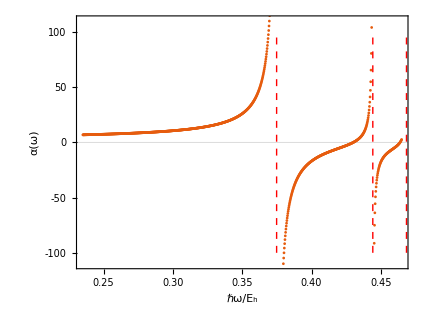
n | E_n0 | Residue
2 | 0.3748 | 0.4164
3 | 0.444207 | 0.079142
4 | 0.4685 | 0.029006
5 | 0.479744 | 0.013945
6 | 0.485852 | 0.0078035
7 | 0.489535 | 0.0048164
8 | 0.491925 | 0.003185
9 | 0.493564 | 0.0022172
10 | 0.494736 | 0.0016062    -Graphics-

```mathematica
Row[{toGrid[modelVals],"    ",plt[modelData,lines[modelVals]]},ImageSize->1000]
```

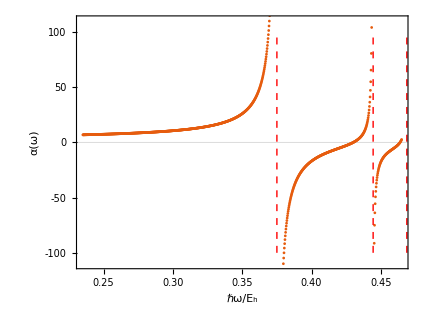
n | E_n0 | Residue
2 | 0.375 | 0.416197
3 | 0.444444 | 0.0791016
4 | 0.46875 | 0.028991
5 | 0.48 | 0.0139383
6 | 0.486111 | 0.00779949
7 | 0.489796 | 0.00481238
8 | 0.492188 | 0.00318343
9 | 0.493827 | 0.00221611
10 | 0.495 | 0.00160537    -Graphics-

```mathematica
Row[{toGrid[exactVals],"    ",plt[modelData,lines[exactVals]]},ImageSize->1000]
```

```mathematica
nterms=20;
col = Table[
    RGBColor[tt/nterms,0, 1 - tt/nterms], {tt, 0,  nterms, nterms/(nterms - 1)}];
```

```mathematica
pDiff[ω_,n_]:=(Abs@(αExact[ω]-αModel[ω,n]))/(Abs@αExact[ω])*100
```

```mathematica
maxerror[n_]:=Assuming[ω>0,Chop@NMaximize[pDiff[I*ω,n],ω]]
pdifDat=Table[{in,Evaluate[maxerror[in][[1]]]},{in,1,nterms}];
```

```mathematica
maxDiff=
ListPlot[
pdifDat,
PlotTheme->"Detailed",
ImageSize -> 375,
PlotRange->Full,
ScalingFunctions->{"Linear","Linear"},
Joined->True,
Mesh->Full,
MeshStyle->Table[ { PointSize[0.025],Evaluate[ColorData[63,"ColorList"]][[ic]]},{ic,Length[Evaluate[ColorData[63,"ColorList"]]]}],
FrameLabel->{"q","Max % Difference"},
LabelStyle -> labStyle[22],
AspectRatio->1,
FrameStyle -> Table[{Thickness[0.007], Black}, {i, 4}],
FrameTicks->Automatic,
PlotStyle->LightGray];
```

```mathematica
pdifPlot=
Plot[
Evaluate[Table[
pDiff[I*ω,in],
{in,1,nterms}]],
{ω,10^-1,11},
PlotTheme->"Scientific",
ImageSize -> 650,
AspectRatio->.75,
PlotRange->{
{-0.1,10.3},
{-0.25,7.3}},
ScalingFunctions->{
"Linear",
"Linear"},
FrameLabel->{
"iℏω/E_h",
"α(iω) % Difference"},
LabelStyle -> labStyle[25],
FrameStyle -> Table[{Thickness[0.0025], Black}, {i, 4}],
FrameTicks->{
linTixSc[0.,7.,1.,1.,1],
linTixSc[0.,10.,2.,1.,1]},
PlotStyle ->Table[ {Thickness[0.001],col[[ic]]},{ic,Length@col}]];
```

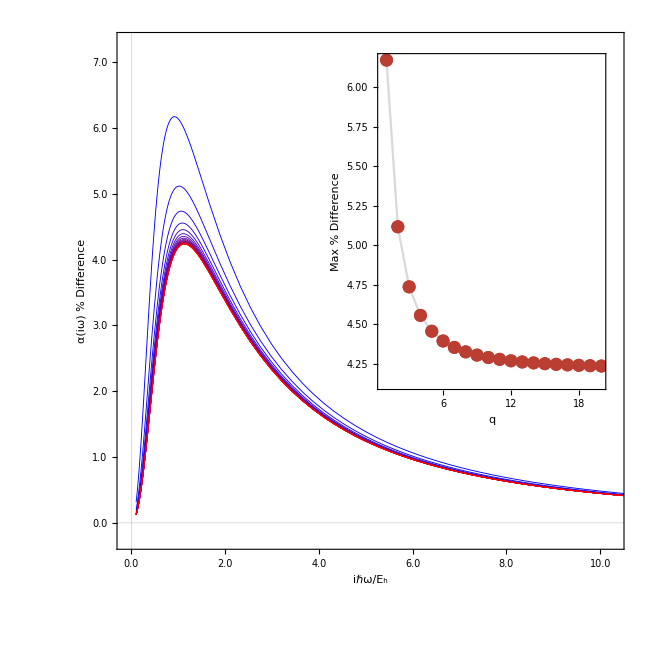

```mathematica
pdifFull=
Show[
Graphics[{
Rectangle[{0,0},{1,1},
pdifPlot],
Rectangle[
{0.50,.30},
{0.95,.95},
maxDiff]},
ImageSize->650,
Background->None],
ImagePadding->{{All,All},{5,375}}]
```

```mathematica
c3TempData=ParallelTable[{(iT-300)/300,(Abs@(c30H[iT]-c30[iT,element->"hydrogen"]))/c30H[iT]*100},{iT,300,1500,(1500-300)/50}];
```

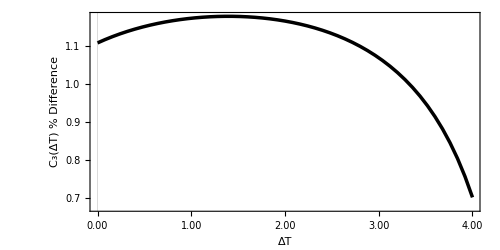

```mathematica
c3per=ListPlot[
c3TempData,
PlotTheme->"Scientific",
ImageSize -> 500,
PlotRange->Full,
ScalingFunctions->{"Linear","Linear"},
Joined->True,
FrameLabel->{"ΔT","C_3(ΔT) % Difference"},
LabelStyle -> labStyle[22],
AspectRatio->0.5,
FrameStyle -> Table[{Thickness[0.004], Black}, {i, 4}],
FrameTicks->{Automatic,linTixScAlt[0.,4.,1.,1]},
PlotStyle->{Thickness[0.005],Black}]
```

```mathematica
extRealPlot=plt[modelData,lines[exactVals]];
```

```mathematica
dirName=FileNameJoin[{FileNameDrop[NotebookDirectory[],-2],"figures","dynPol","hydrogen"}];
```

```mathematica
If [export,Export[FileNameJoin[{dirName,"c3per.eps"}],c3per]];
If [export,Export[FileNameJoin[{dirName,"pdifFull.eps"}],pdifFull]];
If [export,Export[FileNameJoin[{dirName,"exactVals.csv"}],toTeX@exactVals]];
If [export,Export[FileNameJoin[{dirName,"modelVals.csv"}],toTeX@modelVals]];
If [export,Export[FileNameJoin[{dirName,"extRealPlot.eps"}],extRealPlot]];
```